```mathematica
(* baseed on https://syntacticsalt.com/blog/2016-03-07-solving-sudoku-via-sat.html *)
ClearAll["Global`*"];
W=5;U=W^2;

ShowMarking[marking_]:=Module[{},Graphics[Table[{EdgeForm[Thin],If[EvenQ[Floor[(j-1)/W]+Floor[(i-1)/W]],White,Lighter[Gray,0.5]],Rectangle[{i,j},{i+1,j+1}],Black,If[KeyExistsQ[marking,{i,j}],Text[Style[marking[{i,j}],Medium],{i+0.5,j+0.5}]]},{i,1,U},{j,1,U}]]]

ShowSolution[soln_]:=Module[{rarray,r},r=ArrayReshape[soln,{U,U,U}];
rarray=Table[Table[Flatten[Position[r⟦i,j⟧,True]]⟦1⟧,{j,1,U}],{i,1,U}];
Graphics[Table[{EdgeForm[Thin],If[EvenQ[Floor[(j-1)/W]+Floor[(i-1)/W]],White,Lighter[Gray,0.5]],Rectangle[{i,j},{i+1,j+1}],Black,Text[Style[rarray⟦i,j⟧,Medium],{i+0.5,j+0.5}]},{i,1,U},{j,1,U}]]]

s=Table[Table[Table[Unique[s],{z,1,U}],{y,1,U}],{x,1,U}];
AndList[l_]:=Fold[And,True,l];
OrList[l_]:=Fold[Or,False,l];

(* Sudoku rules constraints *)

f1=AndList[Table[AndList[Table[OrList[Table[s[[x,y,i]],{i,1,U}]],{x,1,U}]],{y,1,U}]];
f2=AndList[Table[AndList[Table[AndList[Table[AndList[Table[Not[s[[x,y,z]]]||Not[s[[i,y,z]]],{i,x+1,U}]],{x,1,U-1}]],{z,1,U}]],{y,1,U}]];
f3=AndList[Table[AndList[Table[AndList[Table[AndList[Table[Not[s[[x,y,z]]]||Not[s[[x,i,z]]],{i,y+1,U}]],{y,1,U-1}]],{z,1,U}]],{x,1,U}]];
f4=AndList[Table[AndList[Table[AndList[Table[AndList[Table[AndList[Table[AndList[Table[Not[s⟦W i+x,W j+y,z⟧]||Not[s⟦W i+x,W j+k,z⟧],{k,y+1,W}]],{y,1,W}]],{x,1,W}]],{j,0,W-1}]],{i,0,W-1}]],{z,1,U}]];
f5=AndList[Table[AndList[Table[AndList[Table[AndList[Table[AndList[Table[AndList[Table[AndList[Table[Not[s⟦W i+x,W j+y,z⟧]||Not[s⟦W i+k,W j+l,z⟧],{l,1,W}]],{k,x+1,W}]],{y,1,W}]],{x,1,W}]],{j,0,W-1}]],{i,0,W-1}]],{z,1,U}]];
```

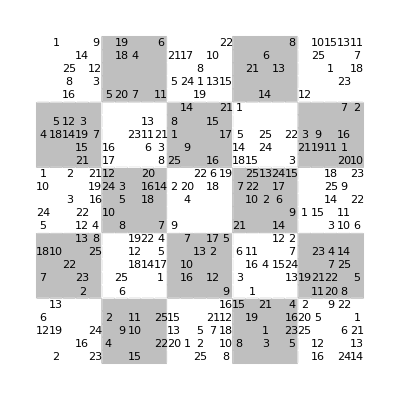

constraint set size: 563125

known problem clues: 253

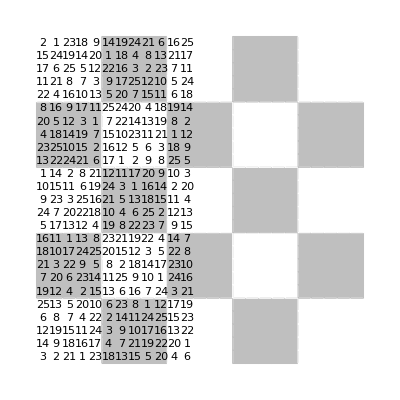

That took 36.8906 seconds.

```mathematica
(* convert matrix to Association form *)
GetAssociationRules[m_?MatrixQ]:=Association@@Reap[With[{b=Dimensions[m]},
Do[If[m⟦i,j⟧≠0,Sow[{i,j}->m⟦i,j⟧]],{i,b⟦1⟧},{j,b⟦2⟧}]]]⟦2⟧;

mymat={{0,0,12,6,0,0,7,0,18,0,5,24,0,10,1,0,0,4,0,0,0,0,0,0,0},{2,0,19,0,13,0,0,0,10,0,0,0,0,0,0,0,0,18,5,0,0,0,0,0,1},{0,0,0,0,0,0,0,22,0,0,0,0,3,0,2,0,0,14,12,0,16,8,25,0,0},{0,16,0,0,0,2,23,0,0,13,12,22,0,0,0,21,15,19,3,0,0,0,0,14,0},{23,0,24,0,0,0,0,0,25,8,4,0,16,19,21,0,0,7,0,0,0,3,12,0,9},{0,4,0,2,0,0,0,0,0,0,0,10,0,24,12,17,16,0,0,0,5,0,0,0,0},{0,0,9,0,0,6,25,0,0,0,8,0,5,3,0,0,0,0,0,0,20,0,0,18,19},{15,0,10,11,0,0,0,18,12,19,0,0,0,0,0,0,0,23,0,0,7,0,0,4,0},{0,0,0,0,0,0,0,14,0,22,0,0,18,16,20,0,6,11,13,0,0,0,0,0,0},{0,22,0,25,0,0,1,17,5,4,7,0,0,14,0,8,3,21,0,0,11,0,0,0,6},{0,20,13,15,0,0,0,0,0,0,9,0,0,2,0,25,0,1,8,0,0,5,0,21,0},{0,1,0,0,0,0,16,10,0,7,0,0,4,20,0,0,9,0,0,14,0,24,0,17,0},{25,2,5,0,0,0,0,0,13,0,0,0,0,0,22,0,0,0,0,0,19,1,8,0,0},{0,0,7,21,0,0,12,0,2,17,0,0,0,18,6,16,0,0,15,0,0,13,0,10,0},{8,10,18,12,16,9,0,0,0,5,0,0,0,0,19,0,0,17,0,21,0,15,0,0,22},{0,8,0,0,15,0,3,0,6,0,21,0,0,7,0,18,14,5,0,1,0,0,0,0,0},{0,0,0,19,0,1,0,16,11,0,0,0,10,22,25,15,0,0,0,0,0,0,21,0,0},{0,3,1,0,21,0,0,4,0,0,0,0,2,0,13,0,24,25,0,0,14,0,0,6,0},{0,0,0,0,0,0,0,15,0,12,14,0,6,17,24,0,0,0,0,0,0,0,13,0,0},{0,5,23,16,4,0,13,24,7,2,0,9,0,0,15,3,0,22,0,0,0,0,0,0,8},{0,0,25,20,2,0,19,0,0,0,0,1,0,0,0,0,21,3,0,0,12,0,0,0,0},{16,12,0,5,0,11,21,0,23,0,0,15,0,0,0,0,19,9,0,0,0,0,0,25,10},{0,0,0,0,9,20,22,7,4,0,3,0,14,25,18,0,11,0,0,0,0,0,1,0,15},{24,0,6,0,22,8,0,25,14,0,10,11,0,9,0,20,1,16,0,7,0,23,0,0,13},{14,13,21,1,0,0,5,0,0,0,6,0,22,0,23,10,0,0,0,2,0,0,18,7,11}};

initial=GetAssociationRules[mymat];
fInit=AndList[Map[s⟦#⟦1⟧,#⟦2⟧,initial[#]⟧&,Keys[initial]]];
ShowMarking[initial]
Print["constraint set size: "<>ToString[Length[Flatten[f1&&f2&&f3&&f4&&f5]]]];
Print["known problem clues: "<>ToString[Length[initial]]];
soln=Timing[SatisfiabilityInstances[f1&&f2&&f3&&f4&&f5&&fInit,Flatten[s]]];
(* r=ArrayReshape[soln,{U,U,U}];
Table[Table[Flatten[Position[r[[i,j]],True]][[1]],{j,1,U}],{i,1,U}]//TableForm *)
ShowSolution[soln⟦2⟧]
Print["That took "<>ToString[soln⟦1⟧]<>" seconds."];
```

Need to create routines for:
	1. convert puzzle to canonical form
	2. search for minimal clue puzzles
		a. remove two, insert one until only one solution exists
	3. database search
		a. special case for puzzles with < 256 states: single line per solution
		b. more general database
	4. ?

```mathematica
(* assume starting puzzle has been solved by above solver, now we want to find other puzzles with fewer clues,
	1. add rules until solvable,
		a. check clues < best,
		b. check solution count is one,
		c. check solution non-dupe,
			print "dupe, but better",
		d. output problem,
	2. remove clues until two under best,
	3. loop to 1.
*)

workclues = Normal[initial];
Subscript[clues, BEST]=Length[workclues];
Subscript[clues, size]=5; (* fix *)
temp=PrintTemporary["Starting..."];
While[True,
(* remove clues randomly *)
While[Length[workclues]≥Subscript[clues, BEST],
workclues=ReplacePart[workclues,RandomInteger[Length[workclues]]->Nothing]];

(* try sudoku, finding two instances quicker than total count *)
aclues=Association[workclues];
soln=SatisfiabilityInstances[f1&&f2&&f3&&f4&&f5&&AndList[Map[s⟦#⟦1⟧,#⟦2⟧,aclues[#]⟧&,Keys[aclues]]],Flatten[s],2];

(* success? *)
If[Length[soln]== 1,
Print[{Length[workclues],workclues}];
Subscript[clues, BEST]=Length[workclues]
];

(* failure, add random rules *)
If[Length[soln]≠1,
While[Length[workclues]≤Subscript[clues, BEST],
j=1;While[j≠0,
n=RandomInteger[{1,Subscript[clues, size]^2}];
x=RandomInteger[{1,Subscript[clues, size]^2}];
y=RandomInteger[{1,Subscript[clues, size]^2}];
j=Count[workclues,{x,y}->_]
+Count[workclues,{x,_}->n]
+Count[workclues,{_,y}->n]
+Count[workclues,{a_,b_}->n
/;Mod[a,Subscript[clues, size]]==Mod[x,Subscript[clues, size]]
&&Mod[b,Subscript[clues, size]]==Mod[y,Subscript[clues, size]]];
];AppendTo[workclues,{x,y}->n];
NotebookDelete[temp];
PrintTemporary["adding "<>ToString[{x,y}->n]];
];
];
];
```

Starting...

```mathematica
Are these any good?
```

{252,{{1,3}→12,{1,4}→6,{1,7}→7,{1,9}→18,{1,11}→5,{1,12}→24,{1,14}→10,{1,15}→1,{1,18}→4,{2,1}→2,{2,3}→19,{2,5}→13,{2,9}→10,{2,18}→18,{2,19}→5,{2,25}→1,{3,8}→22,{3,13}→3,{3,15}→2,{3,18}→14,{3,19}→12,{3,21}→16,{3,22}→8,{3,23}→25,{4,2}→16,{4,6}→2,{4,7}→23,{4,10}→13,{4,11}→12,{4,12}→22,{4,16}→21,{4,17}→15,{4,18}→19,{4,19}→3,{4,24}→14,{5,1}→23,{5,3}→24,{5,9}→25,{5,10}→8,{5,11}→4,{5,13}→16,{5,14}→19,{5,15}→21,{5,18}→7,{5,22}→3,{5,23}→12,{5,25}→9,{6,2}→4,{6,4}→2,{6,12}→10,{6,14}→24,{6,15}→12,{6,16}→17,{6,17}→16,{6,21}→5,{7,3}→9,{7,6}→6,{7,7}→25,{7,11}→8,{7,13}→5,{7,14}→3,{7,21}→20,{7,24}→18,{7,25}→19,{8,1}→15,{8,3}→10,{8,4}→11,{8,8}→18,{8,9}→12,{8,10}→19,{8,18}→23,{8,21}→7,{8,24}→4,{9,8}→14,{9,10}→22,{9,13}→18,{9,14}→16,{9,15}→20,{9,17}→6,{9,18}→11,{9,19}→13,{10,2}→22,{10,4}→25,{10,7}→1,{10,8}→17,{10,9}→5,{10,10}→4,{10,11}→7,{10,14}→14,{10,16}→8,{10,17}→3,{10,18}→21,{10,21}→11,{10,25}→6,{11,2}→20,{11,3}→13,{11,4}→15,{11,11}→9,{11,14}→2,{11,16}→25,{11,18}→1,{11,19}→8,{11,22}→5,{11,24}→21,{12,2}→1,{12,7}→16,{12,8}→10,{12,10}→7,{12,13}→4,{12,14}→20,{12,17}→9,{12,20}→14,{12,22}→24,{12,24}→17,{13,1}→25,{13,2}→2,{13,3}→5,{13,9}→13,{13,15}→22,{13,21}→19,{13,22}→1,{13,23}→8,{14,3}→7,{14,4}→21,{14,7}→12,{14,9}→2,{14,10}→17,{14,14}→18,{14,15}→6,{14,16}→16,{14,19}→15,{14,22}→13,{14,24}→10,{15,1}→8,{15,2}→10,{15,3}→18,{15,4}→12,{15,5}→16,{15,6}→9,{15,10}→5,{15,15}→19,{15,18}→17,{15,20}→21,{15,22}→15,{15,25}→22,{16,2}→8,{16,5}→15,{16,7}→3,{16,9}→6,{16,14}→7,{16,16}→18,{16,17}→14,{16,18}→5,{16,20}→1,{17,4}→19,{17,6}→1,{17,8}→16,{17,9}→11,{17,13}→10,{17,14}→22,{17,15}→25,{17,16}→15,{17,23}→21,{18,2}→3,{18,3}→1,{18,5}→21,{18,8}→4,{18,13}→2,{18,15}→13,{18,17}→24,{18,18}→25,{18,21}→14,{18,24}→6,{19,8}→15,{19,10}→12,{19,11}→14,{19,13}→6,{19,14}→17,{19,15}→24,{19,23}→13,{20,2}→5,{20,3}→23,{20,4}→16,{20,5}→4,{20,7}→13,{20,8}→24,{20,9}→7,{20,10}→2,{20,12}→9,{20,15}→15,{20,16}→3,{20,18}→22,{20,25}→8,{21,3}→25,{21,4}→20,{21,5}→2,{21,7}→19,{21,12}→1,{21,17}→21,{21,18}→3,{21,21}→12,{22,1}→16,{22,2}→12,{22,4}→5,{22,6}→11,{22,7}→21,{22,9}→23,{22,12}→15,{22,17}→19,{22,18}→9,{22,24}→25,{22,25}→10,{23,5}→9,{23,6}→20,{23,7}→22,{23,8}→7,{23,9}→4,{23,11}→3,{23,13}→14,{23,14}→25,{23,15}→18,{23,17}→11,{23,23}→1,{23,25}→15,{24,1}→24,{24,3}→6,{24,5}→22,{24,6}→8,{24,8}→25,{24,9}→14,{24,11}→10,{24,12}→11,{24,14}→9,{24,16}→20,{24,17}→1,{24,18}→16,{24,20}→7,{24,22}→23,{24,25}→13,{25,1}→14,{25,2}→13,{25,3}→21,{25,4}→1,{25,7}→5,{25,11}→6,{25,13}→22,{25,15}→23,{25,16}→10,{25,20}→2,{25,23}→18,{25,24}→7,{25,25}→11}}

{251,{{1,3}→12,{1,4}→6,{1,7}→7,{1,9}→18,{1,11}→5,{1,12}→24,{1,14}→10,{1,15}→1,{1,18}→4,{2,1}→2,{2,3}→19,{2,5}→13,{2,9}→10,{2,18}→18,{2,19}→5,{2,25}→1,{3,8}→22,{3,13}→3,{3,15}→2,{3,18}→14,{3,19}→12,{3,21}→16,{3,22}→8,{3,23}→25,{4,2}→16,{4,6}→2,{4,7}→23,{4,10}→13,{4,11}→12,{4,12}→22,{4,16}→21,{4,17}→15,{4,18}→19,{4,19}→3,{4,24}→14,{5,1}→23,{5,3}→24,{5,9}→25,{5,10}→8,{5,11}→4,{5,13}→16,{5,14}→19,{5,15}→21,{5,18}→7,{5,22}→3,{5,23}→12,{5,25}→9,{6,2}→4,{6,4}→2,{6,12}→10,{6,14}→24,{6,15}→12,{6,16}→17,{6,17}→16,{6,21}→5,{7,3}→9,{7,6}→6,{7,7}→25,{7,11}→8,{7,14}→3,{7,21}→20,{7,24}→18,{7,25}→19,{8,1}→15,{8,3}→10,{8,4}→11,{8,8}→18,{8,9}→12,{8,10}→19,{8,18}→23,{8,21}→7,{8,24}→4,{9,8}→14,{9,10}→22,{9,13}→18,{9,14}→16,{9,15}→20,{9,17}→6,{9,18}→11,{9,19}→13,{10,2}→22,{10,4}→25,{10,7}→1,{10,8}→17,{10,9}→5,{10,10}→4,{10,11}→7,{10,14}→14,{10,16}→8,{10,17}→3,{10,18}→21,{10,21}→11,{10,25}→6,{11,2}→20,{11,3}→13,{11,4}→15,{11,11}→9,{11,14}→2,{11,16}→25,{11,18}→1,{11,19}→8,{11,22}→5,{11,24}→21,{12,2}→1,{12,7}→16,{12,8}→10,{12,10}→7,{12,13}→4,{12,14}→20,{12,17}→9,{12,20}→14,{12,22}→24,{12,24}→17,{13,1}→25,{13,2}→2,{13,3}→5,{13,9}→13,{13,15}→22,{13,21}→19,{13,22}→1,{13,23}→8,{14,3}→7,{14,4}→21,{14,7}→12,{14,9}→2,{14,10}→17,{14,14}→18,{14,15}→6,{14,16}→16,{14,19}→15,{14,22}→13,{14,24}→10,{15,1}→8,{15,2}→10,{15,3}→18,{15,4}→12,{15,5}→16,{15,6}→9,{15,10}→5,{15,15}→19,{15,18}→17,{15,20}→21,{15,22}→15,{15,25}→22,{16,2}→8,{16,5}→15,{16,7}→3,{16,9}→6,{16,14}→7,{16,16}→18,{16,17}→14,{16,18}→5,{16,20}→1,{17,4}→19,{17,6}→1,{17,8}→16,{17,9}→11,{17,13}→10,{17,14}→22,{17,15}→25,{17,16}→15,{17,23}→21,{18,2}→3,{18,3}→1,{18,5}→21,{18,8}→4,{18,13}→2,{18,15}→13,{18,17}→24,{18,18}→25,{18,21}→14,{18,24}→6,{19,8}→15,{19,10}→12,{19,11}→14,{19,13}→6,{19,14}→17,{19,15}→24,{19,23}→13,{20,2}→5,{20,3}→23,{20,4}→16,{20,5}→4,{20,7}→13,{20,8}→24,{20,9}→7,{20,10}→2,{20,12}→9,{20,15}→15,{20,16}→3,{20,18}→22,{20,25}→8,{21,3}→25,{21,4}→20,{21,5}→2,{21,7}→19,{21,12}→1,{21,17}→21,{21,18}→3,{21,21}→12,{22,1}→16,{22,2}→12,{22,4}→5,{22,6}→11,{22,7}→21,{22,9}→23,{22,12}→15,{22,17}→19,{22,18}→9,{22,24}→25,{22,25}→10,{23,5}→9,{23,6}→20,{23,7}→22,{23,8}→7,{23,9}→4,{23,11}→3,{23,13}→14,{23,14}→25,{23,15}→18,{23,17}→11,{23,23}→1,{23,25}→15,{24,1}→24,{24,3}→6,{24,5}→22,{24,6}→8,{24,8}→25,{24,9}→14,{24,11}→10,{24,12}→11,{24,14}→9,{24,16}→20,{24,17}→1,{24,18}→16,{24,20}→7,{24,22}→23,{24,25}→13,{25,1}→14,{25,2}→13,{25,3}→21,{25,4}→1,{25,7}→5,{25,11}→6,{25,13}→22,{25,15}→23,{25,16}→10,{25,20}→2,{25,23}→18,{25,24}→7,{25,25}→11}}

{250,{{1,3}→12,{1,4}→6,{1,7}→7,{1,9}→18,{1,11}→5,{1,12}→24,{1,14}→10,{1,15}→1,{1,18}→4,{2,1}→2,{2,3}→19,{2,5}→13,{2,9}→10,{2,18}→18,{2,19}→5,{2,25}→1,{3,8}→22,{3,13}→3,{3,15}→2,{3,18}→14,{3,19}→12,{3,21}→16,{3,22}→8,{3,23}→25,{4,2}→16,{4,6}→2,{4,7}→23,{4,10}→13,{4,11}→12,{4,12}→22,{4,16}→21,{4,17}→15,{4,18}→19,{4,19}→3,{5,1}→23,{5,3}→24,{5,9}→25,{5,10}→8,{5,11}→4,{5,13}→16,{5,14}→19,{5,15}→21,{5,18}→7,{5,22}→3,{5,23}→12,{5,25}→9,{6,2}→4,{6,4}→2,{6,12}→10,{6,14}→24,{6,15}→12,{6,16}→17,{6,17}→16,{6,21}→5,{7,3}→9,{7,6}→6,{7,7}→25,{7,11}→8,{7,14}→3,{7,21}→20,{7,24}→18,{7,25}→19,{8,1}→15,{8,3}→10,{8,4}→11,{8,8}→18,{8,9}→12,{8,10}→19,{8,18}→23,{8,21}→7,{8,24}→4,{9,8}→14,{9,10}→22,{9,13}→18,{9,14}→16,{9,15}→20,{9,17}→6,{9,18}→11,{9,19}→13,{10,2}→22,{10,4}→25,{10,7}→1,{10,8}→17,{10,9}→5,{10,10}→4,{10,11}→7,{10,14}→14,{10,16}→8,{10,17}→3,{10,18}→21,{10,21}→11,{10,25}→6,{11,2}→20,{11,3}→13,{11,4}→15,{11,11}→9,{11,14}→2,{11,16}→25,{11,18}→1,{11,19}→8,{11,22}→5,{11,24}→21,{12,2}→1,{12,7}→16,{12,8}→10,{12,10}→7,{12,13}→4,{12,14}→20,{12,17}→9,{12,20}→14,{12,22}→24,{12,24}→17,{13,1}→25,{13,2}→2,{13,3}→5,{13,9}→13,{13,15}→22,{13,21}→19,{13,22}→1,{13,23}→8,{14,3}→7,{14,4}→21,{14,7}→12,{14,9}→2,{14,10}→17,{14,14}→18,{14,15}→6,{14,16}→16,{14,19}→15,{14,22}→13,{14,24}→10,{15,1}→8,{15,2}→10,{15,3}→18,{15,4}→12,{15,5}→16,{15,6}→9,{15,10}→5,{15,15}→19,{15,18}→17,{15,20}→21,{15,22}→15,{15,25}→22,{16,2}→8,{16,5}→15,{16,7}→3,{16,9}→6,{16,14}→7,{16,16}→18,{16,17}→14,{16,18}→5,{16,20}→1,{17,4}→19,{17,6}→1,{17,8}→16,{17,9}→11,{17,13}→10,{17,14}→22,{17,15}→25,{17,16}→15,{17,23}→21,{18,2}→3,{18,3}→1,{18,5}→21,{18,8}→4,{18,13}→2,{18,15}→13,{18,17}→24,{18,18}→25,{18,21}→14,{18,24}→6,{19,8}→15,{19,10}→12,{19,11}→14,{19,13}→6,{19,14}→17,{19,15}→24,{19,23}→13,{20,2}→5,{20,3}→23,{20,4}→16,{20,5}→4,{20,7}→13,{20,8}→24,{20,9}→7,{20,10}→2,{20,12}→9,{20,15}→15,{20,16}→3,{20,18}→22,{20,25}→8,{21,3}→25,{21,4}→20,{21,5}→2,{21,7}→19,{21,12}→1,{21,17}→21,{21,18}→3,{21,21}→12,{22,1}→16,{22,2}→12,{22,4}→5,{22,6}→11,{22,7}→21,{22,9}→23,{22,12}→15,{22,17}→19,{22,18}→9,{22,24}→25,{22,25}→10,{23,5}→9,{23,6}→20,{23,7}→22,{23,8}→7,{23,9}→4,{23,11}→3,{23,13}→14,{23,14}→25,{23,15}→18,{23,17}→11,{23,23}→1,{23,25}→15,{24,1}→24,{24,3}→6,{24,5}→22,{24,6}→8,{24,8}→25,{24,9}→14,{24,11}→10,{24,12}→11,{24,14}→9,{24,16}→20,{24,17}→1,{24,18}→16,{24,20}→7,{24,22}→23,{24,25}→13,{25,1}→14,{25,2}→13,{25,3}→21,{25,4}→1,{25,7}→5,{25,11}→6,{25,13}→22,{25,15}→23,{25,16}→10,{25,20}→2,{25,23}→18,{25,24}→7,{25,25}→11}}

{249,{{1,3}→12,{1,4}→6,{1,7}→7,{1,9}→18,{1,11}→5,{1,12}→24,{1,14}→10,{1,15}→1,{1,18}→4,{2,1}→2,{2,3}→19,{2,5}→13,{2,9}→10,{2,18}→18,{2,19}→5,{2,25}→1,{3,8}→22,{3,13}→3,{3,15}→2,{3,18}→14,{3,19}→12,{3,21}→16,{3,22}→8,{3,23}→25,{4,2}→16,{4,6}→2,{4,7}→23,{4,10}→13,{4,11}→12,{4,12}→22,{4,16}→21,{4,17}→15,{4,18}→19,{4,19}→3,{5,1}→23,{5,3}→24,{5,9}→25,{5,10}→8,{5,11}→4,{5,13}→16,{5,14}→19,{5,15}→21,{5,18}→7,{5,22}→3,{5,23}→12,{5,25}→9,{6,2}→4,{6,4}→2,{6,12}→10,{6,14}→24,{6,15}→12,{6,16}→17,{6,17}→16,{6,21}→5,{7,3}→9,{7,6}→6,{7,7}→25,{7,11}→8,{7,14}→3,{7,21}→20,{7,24}→18,{7,25}→19,{8,1}→15,{8,3}→10,{8,4}→11,{8,8}→18,{8,10}→19,{8,18}→23,{8,21}→7,{8,24}→4,{9,8}→14,{9,10}→22,{9,13}→18,{9,14}→16,{9,15}→20,{9,17}→6,{9,18}→11,{9,19}→13,{10,2}→22,{10,4}→25,{10,7}→1,{10,8}→17,{10,9}→5,{10,10}→4,{10,11}→7,{10,14}→14,{10,16}→8,{10,17}→3,{10,18}→21,{10,21}→11,{10,25}→6,{11,2}→20,{11,3}→13,{11,4}→15,{11,11}→9,{11,14}→2,{11,16}→25,{11,18}→1,{11,19}→8,{11,22}→5,{11,24}→21,{12,2}→1,{12,7}→16,{12,8}→10,{12,10}→7,{12,13}→4,{12,14}→20,{12,17}→9,{12,20}→14,{12,22}→24,{12,24}→17,{13,1}→25,{13,2}→2,{13,3}→5,{13,9}→13,{13,15}→22,{13,21}→19,{13,22}→1,{13,23}→8,{14,3}→7,{14,4}→21,{14,7}→12,{14,9}→2,{14,10}→17,{14,14}→18,{14,15}→6,{14,16}→16,{14,19}→15,{14,22}→13,{14,24}→10,{15,1}→8,{15,2}→10,{15,3}→18,{15,4}→12,{15,5}→16,{15,6}→9,{15,10}→5,{15,15}→19,{15,18}→17,{15,20}→21,{15,22}→15,{15,25}→22,{16,2}→8,{16,5}→15,{16,7}→3,{16,9}→6,{16,14}→7,{16,16}→18,{16,17}→14,{16,18}→5,{16,20}→1,{17,4}→19,{17,6}→1,{17,8}→16,{17,9}→11,{17,13}→10,{17,14}→22,{17,15}→25,{17,16}→15,{17,23}→21,{18,2}→3,{18,3}→1,{18,5}→21,{18,8}→4,{18,13}→2,{18,15}→13,{18,17}→24,{18,18}→25,{18,21}→14,{18,24}→6,{19,8}→15,{19,10}→12,{19,11}→14,{19,13}→6,{19,14}→17,{19,15}→24,{19,23}→13,{20,2}→5,{20,3}→23,{20,4}→16,{20,5}→4,{20,7}→13,{20,8}→24,{20,9}→7,{20,10}→2,{20,12}→9,{20,15}→15,{20,16}→3,{20,18}→22,{20,25}→8,{21,3}→25,{21,4}→20,{21,5}→2,{21,7}→19,{21,12}→1,{21,17}→21,{21,18}→3,{21,21}→12,{22,1}→16,{22,2}→12,{22,4}→5,{22,6}→11,{22,7}→21,{22,9}→23,{22,12}→15,{22,17}→19,{22,18}→9,{22,24}→25,{22,25}→10,{23,5}→9,{23,6}→20,{23,7}→22,{23,8}→7,{23,9}→4,{23,11}→3,{23,13}→14,{23,14}→25,{23,15}→18,{23,17}→11,{23,23}→1,{23,25}→15,{24,1}→24,{24,3}→6,{24,5}→22,{24,6}→8,{24,8}→25,{24,9}→14,{24,11}→10,{24,12}→11,{24,14}→9,{24,16}→20,{24,17}→1,{24,18}→16,{24,20}→7,{24,22}→23,{24,25}→13,{25,1}→14,{25,2}→13,{25,3}→21,{25,4}→1,{25,7}→5,{25,11}→6,{25,13}→22,{25,15}→23,{25,16}→10,{25,20}→2,{25,23}→18,{25,24}→7,{25,25}→11}}

$Aborted